# Agent Network

## Create Base/Seed Network

```mathematica
network[nodes_,conn_]:=Flatten[Table[Table[i->Mod[i+j,nodes,1],{i,1,If[j≥Quotient[nodes+1,2],nodes/2,nodes],1}],{j,1,conn-1,1}]]
```

#### Degree Computation for base network

```mathematica
k = network[10,3]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→1,1→3,2→4,3→5,4→6,5→7,6→8,7→9,8→10,9→1,10→2}

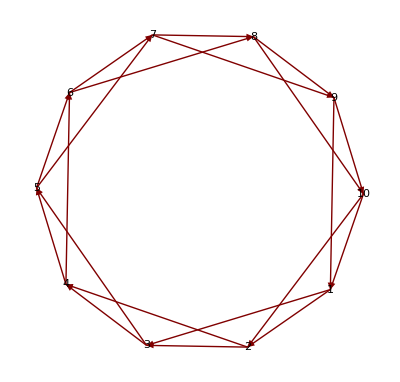

```mathematica
GraphPlot[k,DirectedEdges->True,VertexLabeling->True]
```

```mathematica
Length[k]
```

20

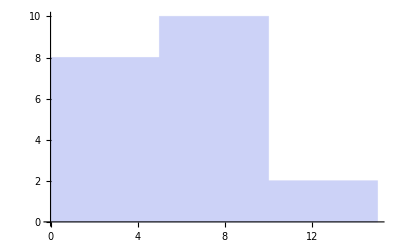

```mathematica
Histogram[k]
```

```mathematica
Needs["Combinatorica`"]
d = For[i = 1, i<Length[k]+1, i++, Distribution[k,{i->j_}]]
```

```mathematica
Distribution[k,{2->j_}]
```

{2}

## Recalibrating connections

```mathematica
network2 = rewirednetwork[p_,network_]:=Table[If[RandomReal[]>p,network[[i]],network[[i]][[1]]->RandomChoice[Cases[network[[All,2]],Except[network[[i]][[1]]]]]],{i,Dimensions[network][[1]]}]
```

```mathematica
k2 = rewirednetwork[0.23,network[1000,3]];
```

```mathematica
Length[k2]
```

2000

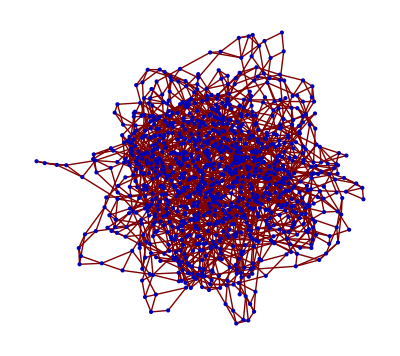

```mathematica
GraphPlot[k2,DirectedEdges->False,VertexLabeling->False]
```

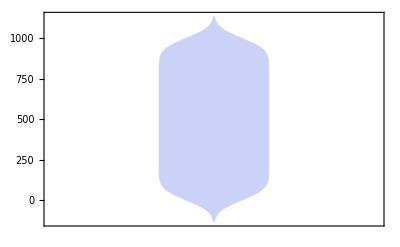

```mathematica
DistributionChart[k2]
```